```mathematica
SetDirectory @ NotebookDirectory[];
Import["QuEST.m"];
Install["quest_link_GPU"];
```

Circuit generation

```mathematica
getHamil[n_] :=
	Table[Subscript[σ, q-1] Subscript[σ, Mod[q,n]],{σ,{X,Y,Z}},{q,n}] ~Join~ Table[RandomReal[{-1,1}] Subscript[Z, q-1],{q,n}] // Flatten
symmetrize[hamil_List, λ_, 1] := (λ hamil)
symmetrize[hamil_List, λ_, 2] := With[{s1 = symmetrize[hamil, λ/2, 1]}, Join[s1,Reverse[s1]]]
symmetrize[hamil_List, λ_, n_?EvenQ] := 
	Block[{γ, p=1/(4-4^(1/(n-1)))}, 
		With[{s=symmetrize[hamil,γ,n-2]}, {r=s /. γ -> λ p},
			Join[r, r, s /. γ -> (1-4p)λ, r, r]]]
trotterize[hamil_List, order_, reps_, time_] :=
	With[{s=symmetrize[hamil, N @ time/reps, order]},
		Flatten @ ConstantArray[s, reps]]
getGate[Verbatim[Times][θ:_?NumericQ:1, σ:__]] := R[2 θ, Times[σ]]
getCircuit[terms_List] := getGate /@ terms
```

```mathematica
numQb = 10;
inCircuit = getCircuit @ trotterize[getHamil[numQb],1,1,2];
DrawCircuit[inCircuit]
```

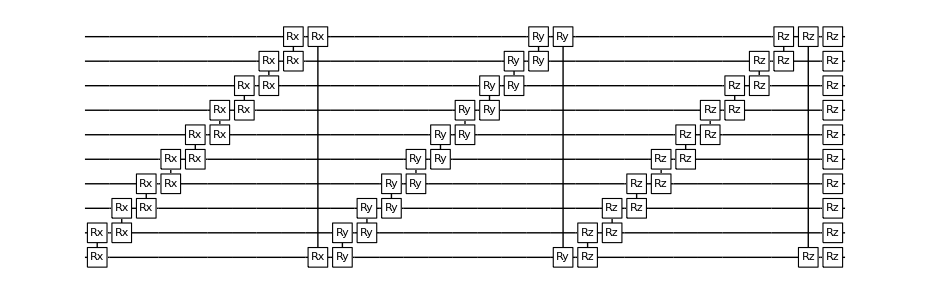

```mathematica
outCircuit = MapIndexed[inCircuit⟦#1⟧/.R[ϕ_,σ___]:>R[Subscript[θ, #2⟦1⟧],σ]& , Range@Length@inCircuit];
AppendTo[outCircuit, G[Subscript[θ, Length[outCircuit]+1]]];
DrawCircuit[outCircuit, numQb]
```

```mathematica
numParams = Length[outCircuit];
ψ = CreateQureg[numQb];
dψ = CreateQuregs[numQb, numParams];
```

Optimised energy calculations under Hamiltonian 1 - |0><0|

```mathematica
calcEnergy[ψ_] :=
	1 - Abs[GetAmp[ψ, 0]]^2

calcEnergyGrad[ψ_, dψ_] :=
	Table[Re[CalcInnerProduct[ψ,dψdp] - Conjugate[GetAmp[ψ,0]] GetAmp[dψdp,0]],{dψdp, dψ}]
```

Dynamic time-step adaptation

```mathematica
paramMapper = MapIndexed[Subscript[θ, #2⟦1⟧]->#1&];

sampleTimestep[Δt_, θ_, Δθ_, prevE_] := (
	ApplyCircuit[outCircuit /. paramMapper[θ + Δt Δθ], InitZeroState[ψ]];
	calcEnergy[ψ] - prevE)

sampleTimesteps[Δt_, θ_, Δθ_, prevE_, {None,None,None}] :=
	Table[
		sampleTimestep[Δtchoice, θ, Δθ, prevE],
		{Δtchoice, {Δt/2, Δt, 2Δt}}];
	
sampleTimesteps[Δt_, θ_, Δθ_, prevE_, samples_List] :=
	If[
		samples⟦1⟧ === None,
		{sampleTimestep[Δt/2,θ, Δθ, prevE], samples⟦2⟧, samples⟦3⟧},
		{samples⟦1⟧, samples⟦2⟧, sampleTimestep[2Δt, θ, Δθ, prevE]}]

chooseTimestep[Δt_, θ_, Δθ_, prevE_, samples_:{None,None,None}] :=
	Module[{tA,tB,tC, tBest},
		{tA,tB,tC} = sampleTimesteps[Δt, θ, Δθ,prevE, samples];
		tBest = Min[tA,tB,tC];
		Which[
			Abs[tBest] < 10^-8,
			Δt,
			tBest > 0,
			chooseTimestep[Δt/8, θ, Δθ, prevE],
			tBest === tC,
			chooseTimestep[2Δt, θ, Δθ, prevE, {tB,tC,None}],
			tBest === tA,
			chooseTimestep[Δt/2, θ, Δθ, prevE, {None,tA,tB}],
			tBest === tB,
			Δt]]
```

Variational imaginary time evolution

```mathematica
simImag[initparams_, steps_, timestep_:Null] := 
	Module[{params, matrA, vecC, energy, Δt, Δθ, energyLog={},paramLog={},ΔtLog={}},
		Δt = If[timestep === Null, 1, timestep];
		params = initparams;
		ApplyCircuit[outCircuit /. params, InitZeroState[ψ]];
		energy = calcEnergy[ψ];
		Do[
			CalcQuregDerivs[outCircuit, InitZeroState[ψ], params, dψ];
			matrA = Re @ CalcInnerProducts[dψ];

			ApplyCircuit[outCircuit /. params, InitZeroState[ψ]];
			vecC = - Re @ calcEnergyGrad[ψ, dψ];

			Δθ = LinearSolve[matrA, vecC, Method->"Krylov"];
			Δt = If[
				timestep === Null,
				chooseTimestep[Δt, params⟦All,2⟧, Δθ, energy],
				timestep];
			params = paramMapper[params⟦All,2⟧ + Δt Δθ];
		
			ApplyCircuit[outCircuit /. params, InitZeroState[ψ]];
			energy = calcEnergy[ψ];
			
			AppendTo[energyLog, energy];
			AppendTo[paramLog, params⟦All,2⟧];
			AppendTo[ΔtLog, Δt];
		
			Null, steps];
			
		{energyLog, paramLog, ΔtLog}]
```

```mathematica
initParams = Table[Subscript[θ, i]->RandomReal[{-π/2,π/2}], {i,numParams}];
```

```mathematica
{eLog, pLog, ΔtLog} = simImag[initParams, 10, 1];

opts = {Joined->True, PlotMarkers->Automatic, PlotRange->{{1,All},All}};
ListLogPlot[eLog, opts, AxesLabel->"energy"];
ListLinePlot[Transpose @ pLog, opts,  AxesLabel->"params"];
Labeled[ListLogPlot[ΔtLog, opts,  AxesLabel->"timestep"], "iterations"];
Column[{%%%,%%,%}]
eLog[[-1]]
```

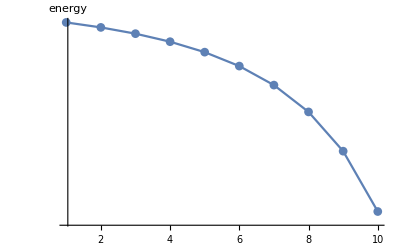
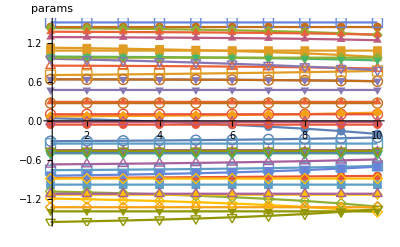
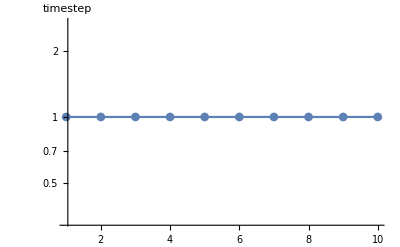
```mathematica
{{-Graphics-}, {-Graphics-}, {-Graphics-"iterations"}}
```

0.975108

LinearSolve::krymit: The maximum number of iterations, 410, has been reached by the Krylov algorithm without convergence to a solution within the required tolerance. The currently computed solution has been returned.

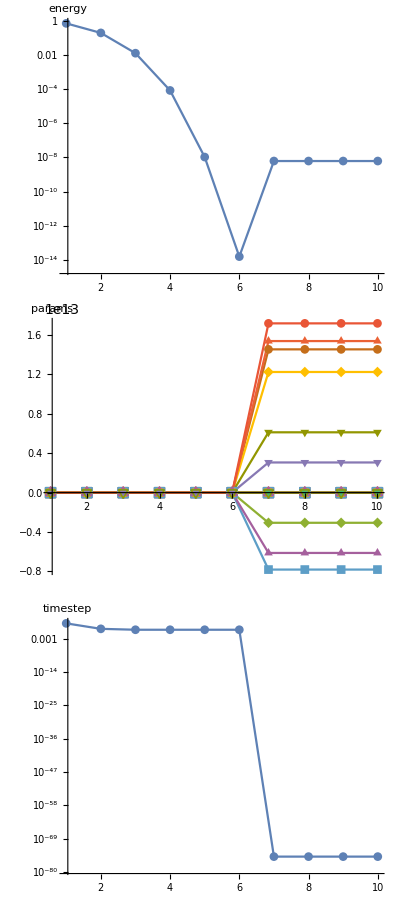

6.14768×10^-9

```mathematica
{eLog, pLog, ΔtLog} = simImag[initParams, 10];
ListLogPlot[eLog, opts, AxesLabel->"energy"];
ListLinePlot[Transpose @ pLog, opts,  AxesLabel->"params"];
ListLogPlot[ΔtLog, opts,  AxesLabel->"timestep"];
Column[{%%%,%%,%}]
eLog[[-1]]
```